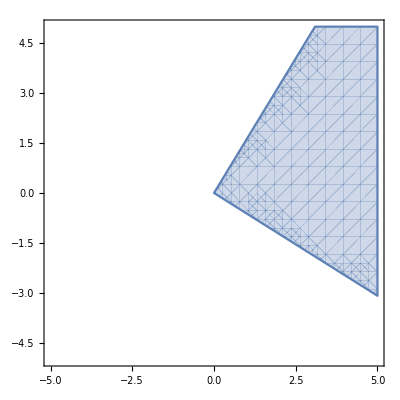

```mathematica
constraintsRule = c -> a + b;
M = ({{a, b}, {b, c}}) //. constraintsRule;
RegionPlot[AllTrue[Eigenvalues[M], # ≥ 0 &], {a, -5, 5}, {b, -5, 5}]
```